```mathematica
ClearAll[P,Ε,EA,u]
P[X_,F_:0]:=Piecewise[{
{50000-F,X≤0.7},
{50000 ,1.0≥ X>0.7}
}
];
 (* in Newtons*)
A[X_]=Piecewise[{
{π(50/2  10^-3)^2,X≤0.7},
{π(30/2  10^-3)^2 ,1.0≥ X>0.7}
}
](*Area, meters^2*)
ClearAll[Ε]
Ε[X_,E1_:200,E2_:200]:=Piecewise[{
{ E1 * 10^9,X≤0.7},
{ E2 *10^9,1.0≥ X>0.7}
}
](*Young's modulus, in Newtons.meters^2*);

EA[X_,E1_:200,E2_:200]:=A[X]Ε[X,E1,E2](*Axial rigidity, in Newtons*);
u[X_,E1_:200,E2_:200,F_:0]:=NIntegrate[P[Y,F]/EA[Y,E1,E2],{Y,0,X}]
```

Piecewise[{{π/1600, X≤0.7}, {(9 π)/40000, 1.≥X>0.7}, {0, True}}]

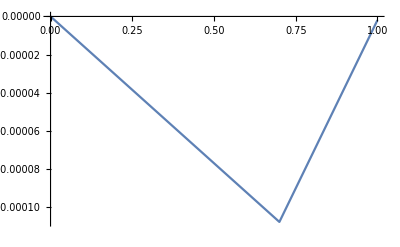

```mathematica
Plot[EA[X],{X,0,1}]
Plot[u[X],{X,0,1}]
```

```mathematica
EA[0.6999,120,200]
```

75000000 π

-0.00174009

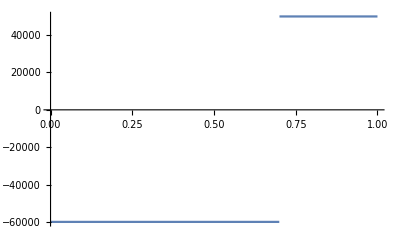

```mathematica
u[1.00,120,200,86.3 10^3] 1000
```

-Graphics-

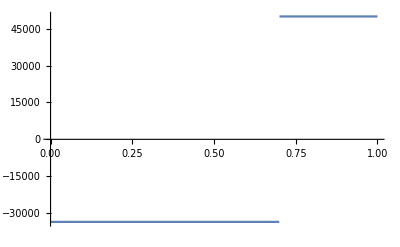

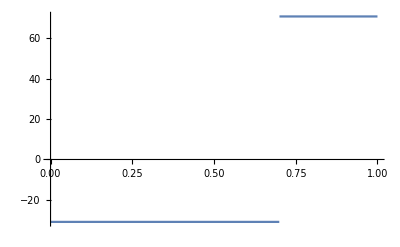

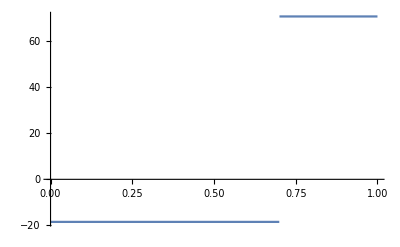

-Graphics-

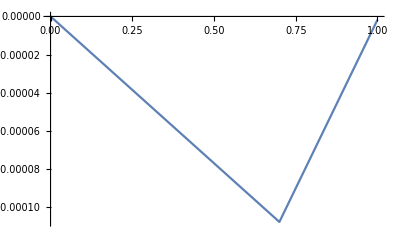

```mathematica
Plot[P[X,110 10^3],{X,0,1}]
Plot[P[X,83.6 10^3],{X,0,1}]
Plot[P[X,110.6 10^3]/A[X]/10^6,{X,0,1}]
Plot[P[X,86.3 10^3]/A[X]/10^6,{X,0,1}]
Plot[u[x,200,200,110.6 10^3],{x,0,1}]
Plot[u[x,120,200,86.3 10^3],{x,0,1}]
```